```mathematica
(*Simulation of scattering rate vs 866 satuation parameter*)
```

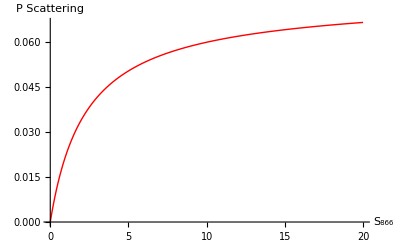

```mathematica
s1 = 0.8(*saturation parameter 397*);H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});H0=H/.{Subscript[Δ, g]->-20,Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];scanredintensity[s_]:=Module[{r,H=H0/.{s2->s},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];data=Table[{s,scanredintensity[s]},{s,0,20,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"S_866","P Scattering"}]
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*For the Mg+ ion
-Graphics-*)
```

```mathematica
U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(280*10^-9))^3)*(2*Pi*41.8*10^6)/(2*Pi*275*10^9)*(190*10^-3)/((7*10^-6)^2);d=5*10^-6(*note: cannot match if use d=7*10^-6*);m=24*1.66*10^-27;kB=1.380649*10^-23;f=√((2*U0)/(m*d^2))/(2*Pi)(*f=ω/(2*Pi)*)
```

162882.

```mathematica
Series[U0*(Exp[(-2*r^2)/((7*10^-6)^2)]),{r,0,5}]
```

5.21598×10^-25-2.12897×10^-14 r^2+0.000434484 r^4+O[r]^6

```mathematica
f=√((2.1289698615561172*^-14)/(0.5*m))/(2*Pi)
```

164536.

```mathematica
(*-Graphics-*)
```

```mathematica
(*For the Yb+ ion
-Graphics-*)
```

```mathematica
U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(369.5*10^-9))^3)*(2*Pi*19.6*10^6)/(2*Pi*15*10^12)*(156*10^-6)/((0.5*10^-6)^2);d=0.0105*10^-6(*note: cannot match if use d=0.5*10^-6*);m=174*1.66*10^-27;kB=1.380649*10^-23;f=√((2*U0)/(m*d^2))/(2*Pi)(*f=ω/(2*Pi)*);h=6.62607015*10^(−34);U0/h
```

2.50263×10^6

```mathematica
Series[U0*(Exp[(-2*r^2)/((0.5*10^-6)^2)]),{r,0,5}]
```

1.65826×10^-27-1.32661×10^-14 r^2+0.0530644 r^4+O[r]^6

```mathematica
f=√((1.3266095277610181*^-14)/(0.5*m))/(2*Pi)
```

48236.7

```mathematica
(*For the Ca+ ion*)
```

```mathematica
U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(422*10^-9)+(3*10^8)/(397*10^-9)))*(1000*10^-6)/((1*10^-6)^2);m=40*1.66*10^-27;kB=1.380649*10^-23;f=√((2*U0)/(m*d^2))/(2*Pi)(*f=ω/(2*Pi)*);h=6.62607015*10^(−34);U0/h
```

1.93348×10^6

```mathematica
Series[U0*(Exp[(-2*r^2)/((1*10^-6)^2)]),{r,0,5}]
```

5241365941891/(42000000000000000000000000000000000000 π^4)-(5241365941891 r^2)/(21000000000000000000000000 π^4)+(5241365941891 r^4)/(21000000000000 π^4)+O[r]^6

```mathematica
f=√((5241365941891/(21000000000000000000000000 π^4))/(0.5*m))/(2*Pi)
```

44214.4

```mathematica
N[2*Pi*(-(3*10^8)/(422*10^-9)+(3*10^8)/(397*10^-9))]
```

2.8128×10^14

```mathematica
(*How to plot things*)
```

```mathematica
power=1000*10^-6(*In terms of W*);wavelength=532(*In terms of nm*);detuning=2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9))(*In terms of Hz*);bwaist=0.5*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(detuning)*power/(bwaist)^2(*Trap depth*);temp=CoefficientList[Series[U0*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]];f=√((Abs[temp])/(0.5*m))/(2*Pi)(*Trap frequency*)
```

85452.9

```mathematica
Clear[power,wavelength,detuning,bwaist]
```

```mathematica
freq[power_,wavelength_,bwaist_]:=√(1/(0.5*m)(Abs[CoefficientList[Series[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]]]))/(2*Pi)
```

```mathematica
freq[1000*10^-6,532,0.5*10^-6]
```

85452.9

```mathematica
Plot3D[freq[power,wavelength,1*10^-6],{power,500*10^-6,3000*10^-6},{wavelength,422,532}]
```

-Graphics3D-

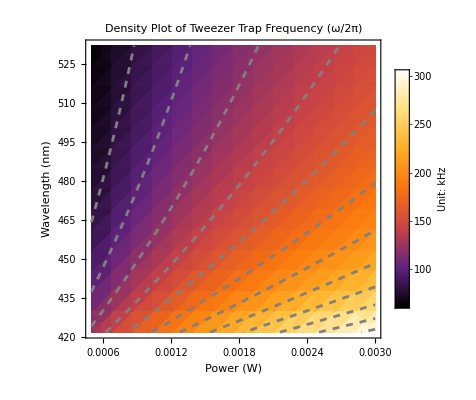

```mathematica
Clear[power,wavelength,detuning,bwaist];bwaist=0.5*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;
zValues=Range[80,300,20];  (*Example range for zValues*)
powermin=500*10^-6;powermax=3000*10^-6;

freq[power_,wavelength_,bwaist_]:=√(1/(0.5*m)(Abs[CoefficientList[Series[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]]]))/(2*Pi*1000);

densityPlot=DensityPlot[freq[power,wavelength,bwaist],{power,powermin,powermax},{wavelength,422,532},ColorFunction->"SunsetColors",MeshStyle->Directive[Dashed,Gray],PlotLegends->BarLegend[Automatic,LegendLabel->"Unit: kHz"],PlotLabel->"Density Plot of Tweezer Trap Frequency (ω/2π)",AxesLabel->{"Power (W)","Wavelength (nm)"}];

contourPlots=ContourPlot[Evaluate@Table[freq[power,wavelength,bwaist]==z,{z,zValues}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Dashed],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

Show[densityPlot,contourPlots]
```

```mathematica
(*Now consider the scattering rate*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
power=1000*10^-6(*In terms of W*);wavelength=532(*In terms of nm*);detuning=2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9))(*In terms of Hz*);bwaist=0.5*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;h=6.62607015*10^(−34);U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(detuning)*power/(bwaist)^2(*Trap depth*);scattering=(1/(7*10^-9))/(detuning*(h/(2*Pi)))*U0
```

1.3451

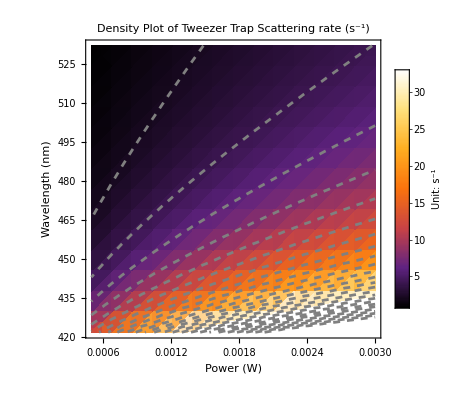

```mathematica
Clear[power,wavelength,detuning,bwaist,scattering];bwaist=0.5*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;
zValues=Range[0,50,2];  (*Example range for zValues*)
powermin=500*10^-6;powermax=3000*10^-6;

scattering[power_,wavelength_,bwaist_]:=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(1/(7*10^-9))/((2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*(h/(2*Pi)));

densityPlot=DensityPlot[scattering[power,wavelength,bwaist],{power,powermin,powermax},{wavelength,422,532},ColorFunction->"SunsetColors",MeshStyle->Directive[Dashed,Gray],PlotLegends->BarLegend[Automatic,LegendLabel->"Unit: s^-1"],PlotLabel->"Density Plot of Tweezer Trap Scattering rate (s^-1)",AxesLabel->{"Power (W)","Wavelength (nm)"}];

contourPlots=ContourPlot[Evaluate@Table[scattering[power,wavelength,bwaist]==z,{z,zValues}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Dashed],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

Show[densityPlot,contourPlots]
```

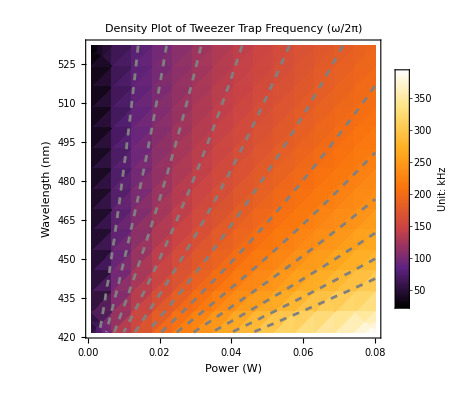

```mathematica
Clear[power,wavelength,detuning,bwaist];bwaist=1*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;
zValues=Range[80,300,20];  (*Example range for zValues*)
powermin=1000*10^-6;powermax=80000*10^-6;

freq[power_,wavelength_,bwaist_]:=√(1/(0.5*m)(Abs[CoefficientList[Series[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]]]))/(2*Pi*1000);

densityPlot=DensityPlot[freq[power,wavelength,bwaist],{power,powermin,powermax},{wavelength,422,532},ColorFunction->"SunsetColors",MeshStyle->Directive[Dashed,Gray],PlotLegends->BarLegend[Automatic,LegendLabel->"Unit: kHz"],PlotLabel->"Density Plot of Tweezer Trap Frequency (ω/2π)",AxesLabel->{"Power (W)","Wavelength (nm)"}];

contourPlots=ContourPlot[Evaluate@Table[freq[power,wavelength,bwaist]==z,{z,zValues}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Dashed],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

Show[densityPlot,contourPlots]
```

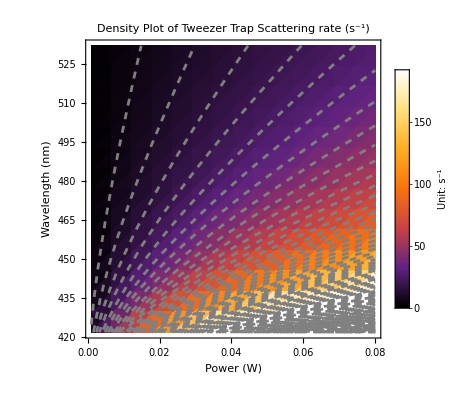

```mathematica
Clear[power,wavelength,detuning,bwaist,scattering];bwaist=1*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;
zValues=Range[0,500,5];  (*Example range for zValues*)
powermin=1000*10^-6;powermax=80000*10^-6;

scattering[power_,wavelength_,bwaist_]:=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(1/(7*10^-9))/((2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*(h/(2*Pi)));

densityPlot=DensityPlot[scattering[power,wavelength,bwaist],{power,powermin,powermax},{wavelength,422,532},ColorFunction->"SunsetColors",MeshStyle->Directive[Dashed,Gray],PlotLegends->BarLegend[Automatic,LegendLabel->"Unit: s^-1"],PlotLabel->"Density Plot of Tweezer Trap Scattering rate (s^-1)",AxesLabel->{"Power (W)","Wavelength (nm)"}];

contourPlots=ContourPlot[Evaluate@Table[scattering[power,wavelength,bwaist]==z,{z,zValues}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Dashed],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

Show[densityPlot,contourPlots]
```

{10}

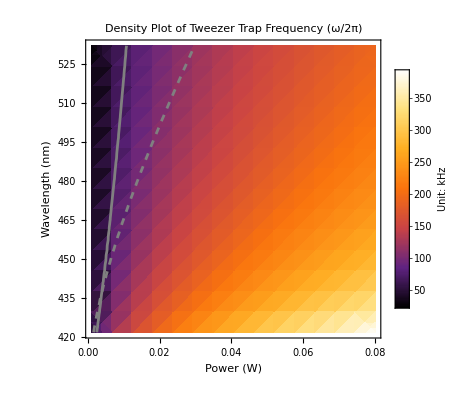

```mathematica
Clear[power,wavelength,detuning,bwaist];bwaist=1*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;
zValues1=Range[70,70,10];  (*Example range for zValues*)
zValues2=Range[10,10,10]
powermin=1000*10^-6;powermax=80000*10^-6;

freq[power_,wavelength_,bwaist_]:=√(1/(0.5*m)(Abs[CoefficientList[Series[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]]]))/(2*Pi*1000);scattering[power_,wavelength_,bwaist_]:=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*power/(bwaist)^2*(1/(7*10^-9))/((2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9)))*(h/(2*Pi)));

densityPlot=DensityPlot[freq[power,wavelength,bwaist],{power,powermin,powermax},{wavelength,422,532},ColorFunction->"SunsetColors",MeshStyle->Directive[Dashed,Gray],PlotLegends->BarLegend[Automatic,LegendLabel->"Unit: kHz"],PlotLabel->"Density Plot of Tweezer Trap Frequency (ω/2π)",AxesLabel->{"Power (W)","Wavelength (nm)"}];

contourPlots1=ContourPlot[Evaluate@Table[freq[power,wavelength,bwaist]==z,{z,zValues1}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Thick],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

contourPlots2=ContourPlot[Evaluate@Table[scattering[power,wavelength,bwaist]==z,{z,zValues2}],{power,powermin,powermax},{wavelength,422,532},ContourStyle->Directive[Gray,Dashed],(*All contours in grey*)ContourLabels->(Text[Style[#3,White],{#1,#2},{-1,-1}]&)];

Show[densityPlot,contourPlots1, contourPlots2]
```

```mathematica
(*How to calculate the trapping force of the given tweezer potential*)
```

```mathematica
power=20*10^-3(*In terms of W*);wavelength=532(*In terms of nm*);detuning=2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9))(*In terms of Hz*);bwaist=1*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(detuning)*power/(bwaist)^2(*Trap depth*);temp=CoefficientList[Series[U0*(Exp[(-2*r^2)/(bwaist)^2]),{r,0,5}],r][[3]];f=√((Abs[temp])/(0.5*m))/(2*Pi)(*Trap frequency*);1/10^6*(N[U0]/(h/(2*Pi)))(*Trap depth*)
```

56.7224

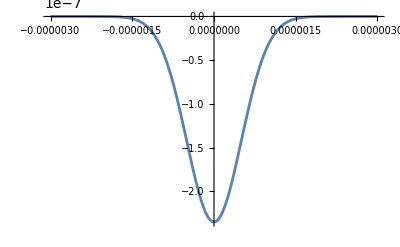

```mathematica
Clear[power,wavelength,detuning,bwaist];power=20*10^-3(*In terms of W*);wavelength=532(*In terms of nm*);detuning=2*Pi*(-(3*10^8)/(wavelength*10^-9)+(3*10^8)/(397*10^-9))(*In terms of Hz*);bwaist=1*10^-6;m=40*1.66*10^-27;kB=1.380649*10^-23;U0=(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(detuning)*power/(bwaist)^2(*Trap depth*);Potential[r_]:=-U0*(Exp[(-2*r^2)/(bwaist)^2]);Plot[1/10^6*Potential[r]/(h/(2*Pi))*10^6*4.14*10^-15,{r,-3*10^-6,3*10^-6}](*Unit is eV and the x axis is m. 1/10^6*Potential[r]/(h/(2*Pi)) means the unit is in MHz.*)
```